```mathematica
NotebookEvaluate[dir<>"mod/Module_CTT.nb"];
invalidncls="[Caution!] An invalid number of student clusters was specified.";
invalidnfld="[Caution!] An invalid number of item fields was specified.";
invalidmodel="[Caution!] An invalid model was selected.";
```

```mathematica
fieldfilecheck[ffile0_]:=Module[{ffile=ffile0},
datacheck[ffile];
confitemlabel=Drop[Import[dir<>ffile],1][[All,1]];
doublelabelcheck[confitemlabel,ffile];
Do[If[MemberQ[itemlabel,confitemlabel[[j]]]==False,Print["[Caution!] An item label that is not used in the data file appears in "<>ffile<>"."];
Exit[]],{j,1,Length[confitemlabel]}];
conffld=Drop[Import[dir<>ffile],1][[All,2]];
conffldmember=Sort[Tally[conffld][[All,1]]];
nfld=Max[conffld];
If[IntegerQ[nfld]==False,Print[invalidnfld];Exit[]];
Do[Which[MemberQ[conffldmember,f]==False,Print["[Caution!] Field "<>ToString[f]<>" has no items."];Exit[],
IntegerQ[conffldmember[[f]]]==False,Print["[Caution!] An invalid field label is used in "<>ffile<>"."];Exit[]],{f,1,nfld}];
conffldmemb=Table[0,{testlength},{nfld}];
Do[conffldmemb[[Position[itemlabel,confitemlabel[[j]]][[1,1]],conffld[[j]]]]=1,{j,1,testlength}];
];
```

```mathematica
drawarrayplot[d0_,c0_,f0_,gamp0_,s0_,col0_]:=Module[{dat=d0,cls=c0,fld=f0,gamp=gamp0,fs=s0,col=col0},
apdata=ArrayPlot[dat,AspectRatio->2,ImageSize->fs];
sz=Length[dat];
jjj=Dimensions[dat][[2]];
fff=Max[fld];
fld01=Table[0,{jjj},{fff}];
Do[fld01[[j,fld[[j]]]]=1,{j,1,jjj}];
ccc=Max[cls];
cls01=Table[0,{sz},{ccc}];
Do[cls01[[i,cls[[i]]]]=1,{i,1,sz}];
fsortdata=Transpose[Flatten[Table[Extract[Transpose[dat],Position[fld,f]],{f,1,fff}],1]];
fcsortdata=Flatten[Table[Extract[fsortdata,Position[cls,c]],{c,1,ccc}],1];
apsortdata=ArrayPlot[fcsortdata,AspectRatio->2,ImageSize->fs];
Nf=Sort[Tally[fld]][[All,2]];
Nc=Sort[Tally[cls]][[All,2]];
cumNf=Table[Sum[Nf[[ff]],{ff,1,f}],{f,1,fff}];
cumNc=Table[Sum[Reverse[Nc][[cc]],{cc,1,c}],{c,1,ccc}];(*Reverse is necessary.*)
vl=Table[Line[{{cumNf[[f]],0},{cumNf[[f]],sz}}],{f,1,fff-1}];
hl=Table[Line[{{0,cumNc[[c]]},{jjj,cumNc[[c]]}}],{c,1,ccc-1}];
vhl=Graphics[{col,Thick,vl,hl}];
aplinedata=Show[apsortdata,vhl];
ccf=Transpose[cls01].dat.fld01;
fcf=Transpose[cls01].(1-dat).fld01;
ncf=ccf+fcf;
pcf=N[(ccf+gamp-1)/(ncf+2gamp-2)];
pcf[[1]]=Table[0,{fff}];
pcf[[-1]]=Table[1,{fff}];
apPcf=ArrayPlot[pcf,AspectRatio->2,ImageSize->fs];
ap={apdata,apsortdata,aplinedata,apPcf}
];
```

```mathematica
(*estpat=0: ordinal biclustering, 1: confirmatory biclustering, 2: confirmatory biclustering in LDB, 3: confirmatory biclustering in BINET*)
biclus[data0_,estpat0_]:=Module[{data=data0,estpat=estpat0},
Off[General::munfl];
itemstat[data];
Which[
estpat==0,
Which[model==1,Print["Biclustering was selected."],
model==2,Print["Ranklustering was selected."],
True,Print[invalidmodel]],
estpat==1,
Which[model==1,Print["Confirmatory biclustering was selected."],
model==2,Print["Confirmatory ranklustering was selected."],
True,Print[invalidmodel]],
estpat==2,
Which[model==1,Print["Local dependenc biclustering was selected."],
model==2,Print["Local dependenc ranklustering was selected."],
True,Print[invalidmodel]]];

ncls=nclus;
Which[ncls<2,Print[invalidncls];Exit[],
ncls>20,Print[invalidncls];Exit[],
IntegerQ[ncls]==False,Print[invalidncls];Exit[]];

If[estpat==0,
Which[nfld<2,Print[invalidnfld];Exit[],
nfld>20,Print[invalidnfld];Exit[],
IntegerQ[nfld]==False,Print[invalidnfld];Exit[]],
fieldfilecheck[fieldfile];
];

If[estpat==3,
zeroscorer=If[minTS==0,1,0];
fullscorer=If[maxTS==testlength,1,0];
If[ncls<zeroscorer+fullscorer+1,Print["[Caution!] The number of classes must be "<>"≥"<>ToString[zeroscorer+fullscorer+1]<>"."];Exit[]]];

maxemt=200;
con=Exp[-testlength];
beta1=1;
beta2=1;
testell=-1/con;
oldtestell=-2/con;
emt=0;
fld0=Ceiling[Table[j,{j,1,testlength}]/(testlength/nfld)];
revcrrsort=Reverse[Sort[Transpose[{crr,Table[j,{j,1,testlength}]}]]][[All,2]];
fld=Sort[Transpose[{revcrrsort,fld0}]][[All,2]];
fldmemb=Table[0,{testlength},{nfld}];(* J*F *)
Table[fldmemb[[j,fld[[j]]]]=1,{j,1,testlength}];
If[estpat≥1,fldmemb=conffldmemb];
pifr=Transpose[N[Transpose[Table[(r+nfld-f)/(ncls+nfld),{f,1,nfld},{r,1,ncls}]]]](* F*R *);
If[estpat==3,
If[zeroscorer==1,pifr[[All,1]]=Table[0,{nfld}]];
If[fullscorer==1,pifr[[All,-1]]=Table[1,{nfld}]]];
(*Print[MatrixForm[pifr]];*)
fil=Which[ncls<5,1.05-.05*ncls,ncls<10,1-0.04*ncls,ncls≥10,0.8-0.02*ncls];
filmat1=DiagonalMatrix[Table[(1-fil)/2,{ncls-1}],1];
filmat2=DiagonalMatrix[Table[fil,{ncls}]];
filmat=filmat1+Transpose[filmat1]+filmat2;
filmat[[1]]=filmat[[1]]/Total[filmat[[1]]];
filmat[[-1]]=filmat[[-1]]/Total[filmat[[-1]]];
filmat=If[model==2,Transpose[filmat],IdentityMatrix[ncls]];
(Label[emtop];
If[Or[testell-oldtestell<=0.0001*Abs[oldtestell],emt==maxemt]==True,Goto[emend]];
emt+=1;
oldtestell=testell;
csr=uuu.fldmemb;(* S*F *)
fsr=(zzz*(1-uuu)).fldmemb;(* S*F *)
llsr=csr.Log[pifr+con]+fsr.Log[1-pifr+con];(* S*R *)
minllsr=Min/@llsr;
expllsr=Exp[llsr-minllsr];
clsmemb=Round[expllsr/Total[expllsr,{2}],.00000001];(* S*R *)
smmemb=clsmemb.filmat;
cjr=Transpose[uuu].smmemb;(* J*R *)
fjr=Transpose[zzz*(1-uuu)].smmemb;(* J*R *)
lljf=cjr.Log[Transpose[pifr]+con]+fjr.Log[Transpose[1-pifr]+con];(* J*F *)
minlljf=Min/@lljf;
explljf=Exp[lljf-minlljf];
fldmemb=Round[explljf/Total[explljf,{2}],.00000001];(* J*F *)
If[estpat≥1,fldmemb=conffldmemb];
cfr=Transpose[fldmemb].Transpose[uuu].smmemb;
ffr=Transpose[fldmemb].Transpose[zzz*(1-uuu)].smmemb;
oldpifr=pifr;
pifr=(cfr+beta1-1)/(cfr+ffr+beta1+beta2-2);
If[estpat==3,
If[zeroscorer==1,pifr[[All,1]]=Table[0,{nfld}]];
If[fullscorer==1,pifr[[All,-1]]=Table[1,{nfld}]]];
If[mic==1,pifr=Sort/@pifr];
testell=Total[cfr*Log[pifr+con]+ffr*Log[1-pifr+con],2];
Print[{emt,testell}];
If[testell-oldtestell≤0,pifr=oldpifr;Goto[emend]];
Goto[emtop];
Label[emend];);

(*Section 7.4 Bicluster Reference Matrix*)
fldnum=Table[f,{f,1,nfld}];
clsnum=Table[r,{r,1,ncls}];
itemnum=Table[j,{j,1,testlength}];
studentnum=Table[s,{s,1,samplesize}];
fldlabel=Table["Field "<>ToString[f],{f,1,nfld}];
frplabel=Table["FRP "<>ToString[f],{f,1,ncls}];
clsname=Table[If[model==2,"Rank ","Class "]<>ToString[c],{c,1,ncls}];
cmplabel=Table["Membership "<>ToString[c],{c,1,ncls}];

(*
fldsort=ReverseSort[Transpose[{Total[pifr,{2}],fldnum}]][[All,2]];
fldmemb=Transpose[Table[fldmemb[[All,fldsort[[f]]]],{f,1,nfld}]];
pifr=Table[pifr[[fldsort[[f]]]],{f,1,nfld}];

clssort=Sort[Transpose[{Total[pifr],clsnum}]][[All,2]];
clsmemb=Transpose[Table[clsmemb[[All,clssort[[r]]]],{r,1,ncls}]];
pifr=Transpose[Table[pifr[[All,clssort[[r]]]],{r,1,ncls}]];
*)

If[estpat≥2,Goto[BiclusEnd]];
NotebookEvaluate[dir<>"mod/Module_IRP.nb"];
fldmembmaxlist=Max/@fldmemb;
fldmemb01=Sign[fldmemb-fldmembmaxlist]+1;
fld=fldmemb01.fldnum;
flddist=Total[fldmemb01];
fldmembdist=Total[fldmemb];
clsmembmaxlist=Max/@clsmemb;
clsmemb01=Sign[clsmemb-clsmembmaxlist]+1;
cls=clsmemb01.clsnum;
rankupodds=Table[If[cls[[s]]==ncls,"",clsmemb[[s,cls[[s]]+1]]/clsmemb[[s,cls[[s]]]]],{s,1,samplesize}];
rankdownodds=Table[If[cls[[s]]==1,"",clsmemb[[s,cls[[s]]-1]]/clsmemb[[s,cls[[s]]]]],{s,1,samplesize}];
clsdist=Total[clsmemb01];
clsmembdist=Total[clsmemb];
testrefprof=Total[pifr*flddist];
woacjudge=Total[Sign[Table[testrefprof[[c+1]]-testrefprof[[c]],{c,1,ncls-1}]]]+1;
pifrout=PadLeft[pifr,{nfld+1,ncls+1},""];
pifrout[[1,2;;-1]]=frplabel;
pifrout[[2;;-1,1]]=fldlabel;
If[model==1,Print["Section 7.4.1 Bicluster Reference Matrix"],Print["Section 7.4.1 Rankluster Reference Matrix"]];
Print[MatrixForm[pifrout]];
pifrcollabelplus={"Latent Field Distribution"};
pifrrowlabelplus=If[model==2,{"Test Reference Profile","Latent Rank Distribution","Rank Membership Distribution"},{"Test Reference Profile","Latent Class Distribution","Class Membership Distribution"}];
pifrout=PadRight[pifrout,{nfld+1+Length[pifrrowlabelplus],ncls+1+Length[pifrcollabelplus]},""];
pifrout[[1,-1]]=pifrcollabelplus[[1]];
pifrout[[-3;;-1,1]]=pifrrowlabelplus;
pifrout[[-3;;-1,2;;1+ncls]]={testrefprof,clsdist,clsmembdist};
pifrout[[2;;1+nfld,-1]]=flddist;

Print["Section 7.4.1 Array Plot"];
arrayplot=drawarrayplot[uuu,cls,fld,1,300,Gray];
apgrid=Grid[{{arrayplot[[1]],arrayplot[[3]]}}];
Print[apgrid];
Export[dir<>"Chapter07ArrayPlot_Original.pdf",arrayplot[[1]]];
Export[dir<>"Chapter07ArrayPlot_Sorted.pdf",arrayplot[[3]]];

Print["Section 7.4.2 Field Reference Profile"];
irpplot[pifr,fldlabel,3,If[model==2,"r","c"]];
Print[clsrefprofile];
Export[dir<>"Chapter07FRP.pdf",clsrefprofile];
irpindex[pifr,fldlabel];
If[model==2,
Print["Section 7.4.2 FRP Indices"];
Print[MatrixForm[irpindexout]];
If[Total[irpindexout[[2;;-1,-2]]]==0,Print["Strongly ordinal alignment condition was satisfied."]]];

trpplot[testrefprof,clsdist,clsmembdist,If[model==2,"r","c"]];
Print[MatrixForm[outputdist]];
If[model==2,
Print["Section 7.4.3 Test Reference Profile (Line) and Latent Rank Distribution (Bar)"],Print["Section 7.4.3 Test Reference Profile (Line) and Latent Class Distribution (Bar)"]];
If[model==2,If[woacjudge==ncls,Print["Weakly ordinal alignment condition was satisfied."]]];
Print[trpfig];
Export[dir<>"Chapter07TRP.pdf",trpfig];
If[model==2,
Print["Section 7.4.7 Latent Rank Distribution (Bar) and Rank Membership Distribution (Line)"],Print["Section 7.4.7 Latent Class Distribution (Bar) and Class Membership Distribution (Line)"]];
Print[lcdfig];
Export[dir<>If[model==2,"Chapter07LRD.pdf","Chapter07LCD.pdf"],lcdfig];

Print["Section 7.4.4 Field Membership Profile"];
fldmembout=PadLeft[fldmemb,{testlength+1,nfld+1},""];
fldmembout[[2;;-1,1]]=itemlabel;
fldmembout[[1,2;;-1]]=fldlabel;
Print[MatrixForm[fldmembout]];
Print["Latent Field Distribution"];
flddistout={fldlabel,flddist};
flddistout=PadLeft[flddistout,{2,nfld+1},""];
flddistout[[2,1]]="N of Items";
Print[MatrixForm[flddistout]];

Print["Section 7.5 Model Fit"];
NotebookEvaluate[dir<>"mod/Module_Modelfit.nb"];
cfr=Transpose[fldmemb].Transpose[uuu].clsmemb;
ffr=Transpose[fldmemb].Transpose[zzz*(1-uuu)].clsmemb;
testell=Total[cfr*Log[pifr+con]+ffr*Log[1-pifr+con],2];
modelnparam=If[model==1,ncls*nfld,Tr[filmat]*nfld];
testfit[zzz,uuu,testell,modelnparam];
testfitinsertpos=Position[testfitout[[All,1]],"Model"][[1,1]];
testfitout[[testfitinsertpos,2]]=If[estpat==0,"","Confirmatory "]<>If[model==1,"Biclustering","Ranklustering"];
testfitout=Insert[testfitout,{"N of Fields",nfld},testfitinsertpos+1];
testfitout=Insert[testfitout,{If[model==1,"N of Classes","N of Ranks"],ncls},testfitinsertpos+2];
oacout={{"Strongly Ordinal Alignment Condition",If[Total[allindices[[All,-2]]]==0,"Satisfied","Unsatisfied"]},
{"Weakly Ordinal Alignment Condition",If[woacjudge==ncls,"Satisfied","Unsatisfied"]}};
If[model==2,testfitout=Join[testfitout,oacout]];
Print[MatrixForm[testfitout]];

biclusterout=PadRight[pifrout,Dimensions[pifrout]+{0,Dimensions[irpindexout][[2]]-1},""];
biclusterout[[1;;nfld+1,-Dimensions[irpindexout][[2]]+1;;-1]]=irpindexout[[All,2;;-1]];
biclusterout=If[model==1,pifrout,biclusterout];
allitemout=Transpose[Join[Transpose[outputitem],Drop[Transpose[fldmembout],1],{Prepend[fld,If[estpat==0,"Latent Field Estimate","Latent Field"]]}]];

outputstudentBicluslabel=Join[cmplabel,{If[model==2,"Latent Rank Estimate","Latent Class Estimate"],"Rank-Up Odds","Rank-Down Odds"}];
outputstudentBiclus=PadRight[outputstudent,{samplesize+1,Length[outputstudentlabel]+Length[outputstudentBicluslabel]},""];
outputstudentBiclus[[1,Length[outputstudentlabel]+1;;-1]]=outputstudentBicluslabel;
outputstudentBiclus[[2;;-1,Length[outputstudentlabel]+1;;Length[outputstudentlabel]+ncls]]=clsmemb;
outputstudentBiclus[[2;;-1,Length[outputstudentlabel]+ncls+1;;-1]]=Transpose[{cls,rankupodds,rankdownodds}];
If[model==1,outputstudentBiclus=outputstudentBiclus[[All,1;;-3]]];
Export[dir<>If[model==1,"Chapter07Biclustering.xlsx","Chapter07Ranklustering.xlsx"],{"Test"->Join[outputtest,testfitout],If[model==1,"Bicluster","Rankluster"]->biclusterout,"Item"->allitemout,"Student"->outputstudentBiclus}];

Label[BiclusEnd];
];
```

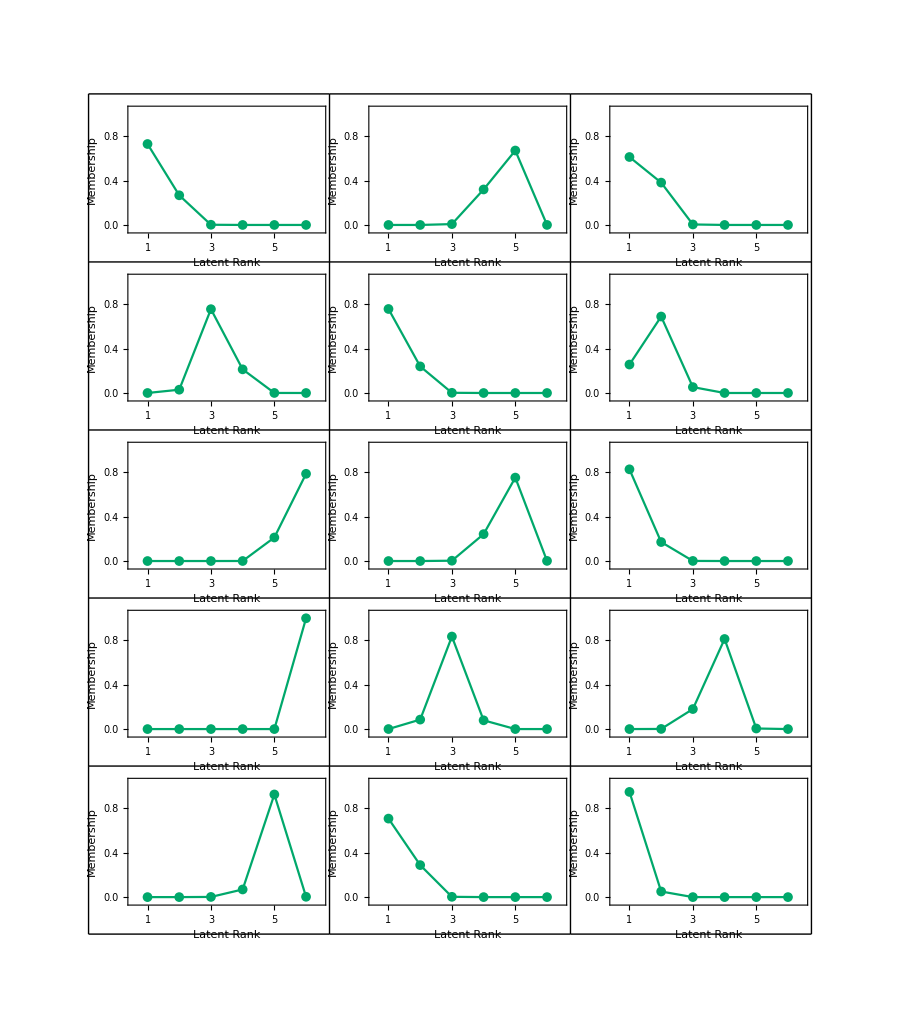

```mathematica
(*figncol=3;
plotnobs=15;
lp=Table[ListPlot[clsmemb[[s]],AxesOrigin->{0,Automatic},LabelStyle->Directive[FontSize->14],PlotStyle->{Directive[RGBColor[0.,168/255,107/255]]},
Frame->True,FrameLabel->{{"Membership",""},{"Latent Rank","Student "<>ToString[s]}},ImageSize->300,PlotRange->{{0.5,nclus+0.5},{-0.05,1.05}},Joined->True,PlotMarkers->{Automatic,Medium},FrameTicks->frticks],{s,1,plotnobs}];
fignrow=Ceiling[plotnobs/figncol];
membershipplot=GraphicsGrid[Table[If[figncol*(r-1)+c≤plotnobs,lp[[figncol*(r-1)+c]],""],{r,1,fignrow},{c,1,figncol}],Frame->All,Spacings->{-15,10},ImageSize->900]
Export[NotebookDirectory[]<>"Fig7.15.pdf",membershipplot];*)
```